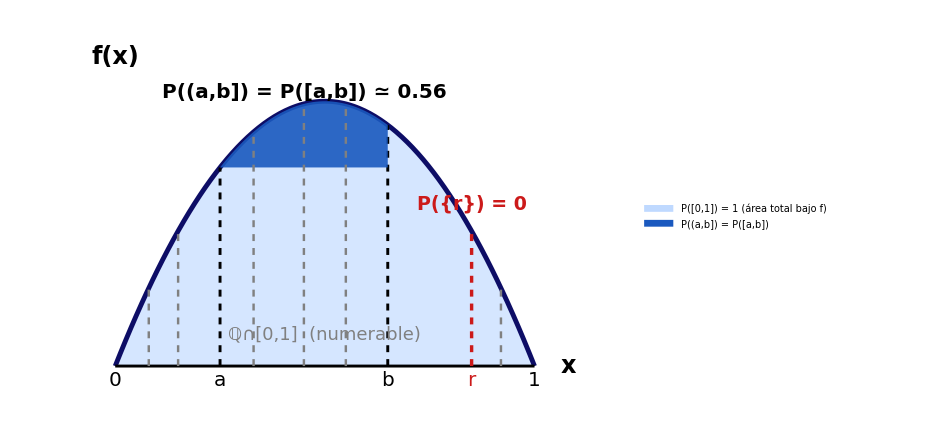

```mathematica
f[x_]:=6 x (1-x);  (*densidad de ejemplo:no negativa,integra 1 en[0,1]*)

a=0.25;b=0.65;rPunto=0.85;
racionales={0.08,0.15,0.33,0.45,0.55,0.92}; (*muestra ilustrativa de Q∩[0,1]*)

colorTotal=RGBColor[0.75,0.85,1];       (*P([0,1])=1*)
colorIntervalo=RGBColor[0.1,0.35,0.75]; (*P((a,b])=P([a,b])*)
colorCurva=RGBColor[0.05,0.05,0.4];
colorR=RGBColor[0.8,0.1,0.1];

pAB=Integrate[f[x],{x,a,b}];

curvaCompleta=Plot[f[x],{x,0,1},Filling->Axis,Axes->False,PlotStyle->Directive[colorCurva,Thickness[0.005]],FillingStyle->Directive[colorTotal,Opacity[0.65]],PlotPoints->80];

areaIntervalo=Plot[f[x],{x,a,b},Filling->Axis,Axes->False,PlotStyle->None,FillingStyle->Directive[colorIntervalo,Opacity[0.9]],PlotPoints->60];

marcasRacionales=Table[{Gray,Dashed,Thickness[0.0025],Line[{{q,0},{q,f[q]}}]},{q,racionales}];

lineaR={colorR,Dashed,Thickness[0.0035],Line[{{rPunto,0},{rPunto,f[rPunto]}}]};
lineasAB={Black,Dashed,Thickness[0.003],Line[{{a,0},{a,f[a]}}],Line[{{b,0},{b,f[b]}}]};

ejeXManual={Black,Thickness[0.003],Line[{{0,0},{1,0}}]};

etiquetas={Text[Style["0",20],{0,-0.08}],Text[Style["a",20],{a,-0.08}],Text[Style["b",20],{b,-0.08}],Text[Style["r",20,colorR],{rPunto,-0.08}],Text[Style["1",20],{1,-0.08}],Text[Style["x",24,Bold],{1.08,0}],Text[Style["f(x)",24,Bold],{0,1.75}],Text[Style["P({r}) = 0",19,Bold,colorR],{rPunto,f[rPunto]+0.15}],Text[Style["P((a,b]) = P([a,b]) ≃ "<>ToString[NumberForm[pAB,{3,2}]],20,Bold],{(a+b)/2,1.55}],Text[Style["ℚ∩[0,1]  (numerable)",18,Italic,Gray],{0.5,0.18}]};

grafico=Show[curvaCompleta,areaIntervalo,Graphics[{ejeXManual,marcasRacionales,lineaR,lineasAB,etiquetas}],PlotRange->{{-0.08,1.2},{-0.15,1.85}},ImageSize->700];

imagenFinal=Legended[grafico,SwatchLegend[{colorTotal,colorIntervalo},{"P([0,1]) = 1  (área total bajo f)","P((a,b]) = P([a,b])"},LabelStyle->Directive[FontSize->20],LegendMarkerSize->22]];

imagenFinal
```

```mathematica
Export["prob_quesada_2_4_a.png",imagenFinal,Background->None,ImageResolution->600];
```

```mathematica
SystemOpen[DirectoryName[AbsoluteFileName["prob_quesada_2_4_a.png"]]]
```